### The photon in a box

Another classic example, only slightly more complex than the free particle, is the particle in a box. For this example, I’ll model a photon with unknown initial position, demonstrate that the same eigenfunctions for the Schrödinger equation work with a Bayesian model.

Again, we need a deterministic model for the photon’s behavior, and it should be as classical as possible. I’ll use a box of unit length, and assume that the photon bounces instantly off the walls on each impact. For a trajectory, we can use x(t)=1-|1-[x(0)+1/2+v(0) (t mod 2)]|-1/2, where the walls of the box are at x=±1/2

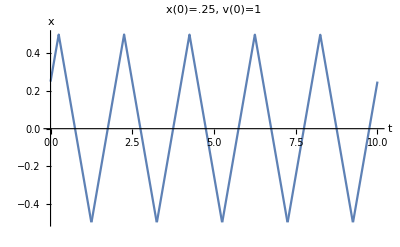

```mathematica
xt[x0_,v0_][t_]:=1-Abs[1-Mod[x0+1/2 +v0 t,2]]-1/2
Plot[xt[.25,1][t],{t,0,10},PlotRange->All,
AxesLabel->{t,x},
PlotLabel->"x(0)=.25, v(0)=1"
]
```

We can ask our physicist friend what the expected steady state results should be. They can tell us that the eigenfunctions for the particle in a box are ψ_n(x)=√2 sin(n π x)e^(i ω t) where n is a natural number. They can further tell us that this means the probability distributions are ψ_n^2(x)=2 sin^2(n π x) (which is just the eigenfunction times its conjugate). Sampling from those distributions is harder than you might expect, since Mathematica is very slow about sampling from arbitrary distributions, especially ones whose CDFs don’t have nice analytic solutions.

To deal with this, we’ll have to be somewhat clever.

```mathematica
$Assumptions={n∈Integers,ω>0,t≥0,x∈Reals};
ψ[n_][x_,t_]:=Sqrt[2]Sin[n π(x+1/2)]Exp[I ω t]
ψ2[n_][x_]:=2 Sin[n π (1/2+x)]^2
```

We could just use rejection sampling, i.e. uniformly generate xs between 0 and 1 and ys between 0 and 2 until we get one where y<ψ_n^2(x), but we can also exploit some symmetries in the distributions to never reject anything. We just need to generate an x between -1/2 and 0, and a y between 0 and 2. If y<ψ_n^2(x), we can accept the x.

For odd ns, if y>ψ^2(x), we can just add 0.5 to x and get the desired distribution, as shown below.

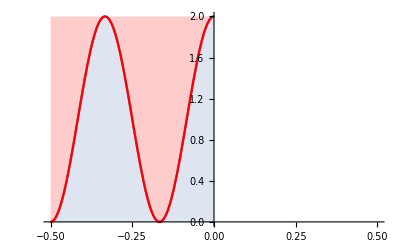

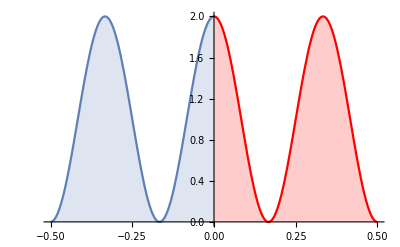

```mathematica
bottom=Plot[ψ2[3][x],{x,-1/2,0},PlotRange->{{-1/2,1/2},All},Filling->Bottom];
top   =Plot[ψ2[3][x],{x,-1/2,0},Filling->Top,PlotStyle->Red];

left = bottom;
right=Plot[ψ2[3][x],{x,0,1/2},Filling->Bottom,PlotStyle->Red];
Show[{bottom,top}]
Show[{left,right}]
```

For even ns, we can do something slightly more complicated. We need to both shift to the right by 0.5, and offset a half period.

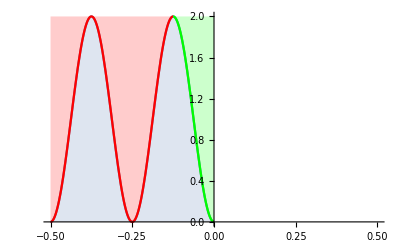

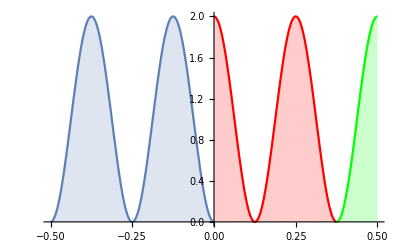

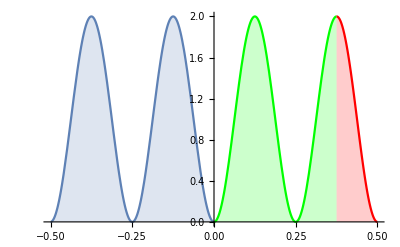

```mathematica
bottom=Plot[ψ2[4][x],{x,-1/2,0},PlotRange->{{-1/2,1/2},All},Filling->Bottom];
top   =Plot[ψ2[4][x],{x,-1/2,-1/8},Filling->Top,PlotStyle->Red];
topLeft=Plot[ψ2[4][x],{x,-1/8,0},Filling->Top,PlotStyle->Green];

left = bottom;
right=Plot[ψ2[4][x-1/8],{x,0,3/8},Filling->Bottom,PlotStyle->Red];
last=Plot[ψ2[4][x-1/8],{x,3/8,1/2},Filling->Bottom,PlotStyle->Green];
Show[{bottom,top,topLeft}]
Show[{left,right,last}]

leftFinal=left;
midFinal=Plot[ψ2[4][x],{x,0,3/8},Filling->Bottom,PlotStyle->Green];
rightFinal=Plot[ψ2[4][x],{x,3/8,1/2},Filling->Bottom,PlotStyle->Red];
Show[{leftFinal,midFinal,rightFinal}]
```

This gives us a system for sampling from our wavefunctions by rejection sampling without any rejection. Pretty neat.

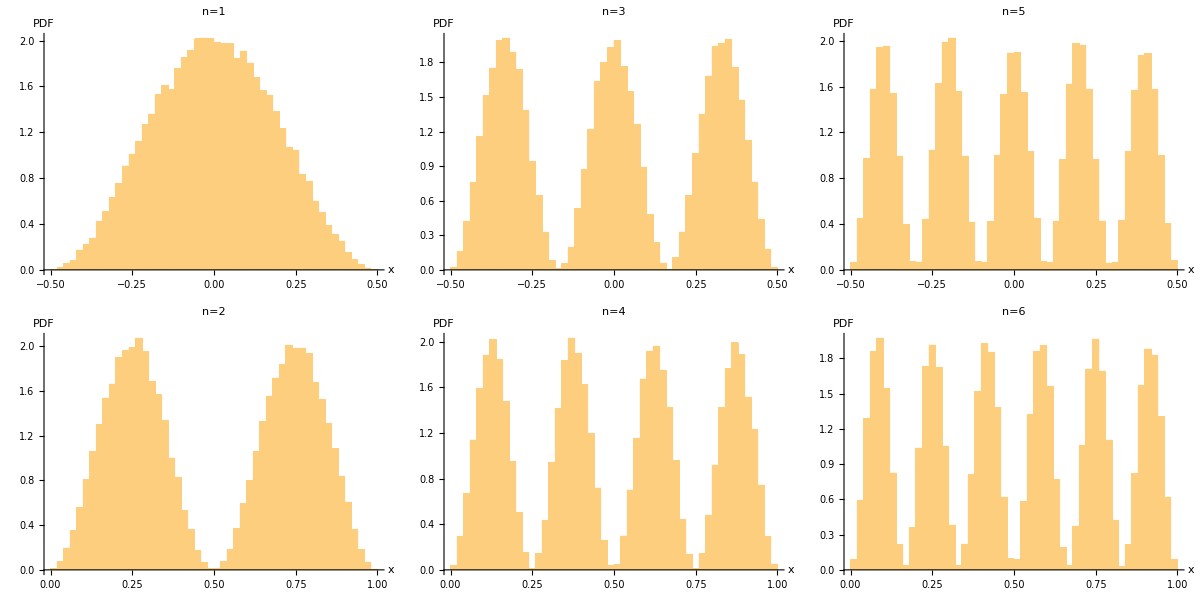

```mathematica
ψSample[n_?OddQ]:=With[{x=RandomReal[{-1/2,0}],y=RandomReal[{0,2}]},
If[y<ψ2[n][x],x,x+1/2]
]
ψSample[n_?EvenQ]:=With[{x=RandomReal[{0,1/2}],y=RandomReal[{0,2}]},
If[y<ψ2[n][x],x,Mod[x+1/(2n),1/2]+1/2]
]
Multicolumn@Table[Histogram[Array[ψSample[n]&,50000],{.02},"PDF",PlotLabel->"n="<>ToString@n,AxesLabel->{x,PDF}],{n,1,6}]
```

Again borrowing from our physicist friend, we know that if we want a standing wave, the momentum should be: -Graphics- 
(from Wikipedia). In this case L=1, and x_c=0, and k=p/ℏ. This is even more unruly than the x distribution, so we’ll just have to evaluate it numerically.

```mathematica
h=1;(*using plank units*)
ℏ=h/(2π);
ϕ[n_][p_]:=Sqrt[1/(π ℏ)]n π/(n π+p/ℏ)Sinc[1/2 (n π-p/ℏ)]
sampleP[n_]:=With[{x=RandomReal[-2n,2n],}]
```

Maximize[(18 π^2 Sinc[1/2 (3 π-2 π x)]^2)/(3 π+2 π x)^2,x]

$Aborted

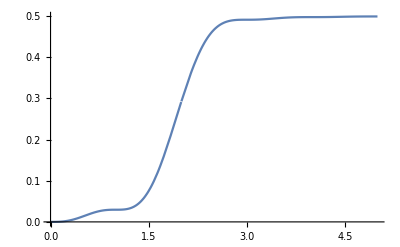

```mathematica
$Assumptions={n∈Integers,ω>0,t≥0,x∈Reals,t>0};
Integrate[ϕ[4][p]^2,{p,0,t}]
Plot[1/(8 π^2 (-4+t^2))(-4 t+4 t Cos[2 π t]+(-4+t^2) CosIntegral[-2 π (-2+t)]-(-4+t^2) CosIntegral[2 π (2+t)]+4 Log[2-t]-t^2 Log[2-t]-4 Log[2+t]+t^2 Log[2+t]-16 π SinIntegral[2 π (2+t)]+4 π t^2 SinIntegral[2 π (2+t)]+16 π SinIntegral[4 π-2 π t]-4 π t^2 SinIntegral[4 π-2 π t]),{t,0,5},PlotRange->All]
```

```mathematica
Manipulate[Plot[ϕ[n][p]^2,{p,-2n,2n},PlotRange->{All,{0,1}}],{n,{1,2,3,4,5,100}}]
```

```mathematica
ensemble=Array[xt[ψSample[3],vSample]&,50000];
ensembleAt[t_]:=#[t]&/@ensemble
Manipulate[Histogram[ensembleAt[t],{.02},"PDF",AxesLabel->{x,PDF}],{t,0,2}]
```